```mathematica
(* tOutDef - рассчетная температура отопления, параметры:
k - коэффициент кривой отопления
 *)
tOutDef[k_]:=-20./k;

(* φ – коэффициент отпуска тепла, параметры:

Константы:
tRoom - требуемая (заданная пользователем) температура внутри помещения,

   Значения с датчиков:
tOut - текущая температура на улице
 *)
φ[tRoom_, tOut_,tOutDef_]:=(tRoom-tOut)/(tRoom-tOutDef);

(* TCalcPod - требуемая температура теплоносителя, параметры:
  
Константы:
tRoom - требуемая (заданная пользователем) температура внутри помещения,
 tPod  - заданная максимальная температура подаваемой воды, обычно до 50 градусов для пола,  до 70 градусов для радиаторов.
 Δt2 – половина нормативной разница между максимальной температурой подачи и обратки. Обычно
это 5 градусов для пола и 7.5 для радиаторов.
  
Значения с датчиков:
tOut - текущая температура на улице
 *)
TCalcPod[tRoom_,tOut_,tOutDef_,Δt2_, tPod_]:=tRoom+(tPod-Δt2-tRoom)φ[tRoom, tOut,tOutDef]^0.76+Δt2 φ[tRoom, tOut,tOutDef];
```

```mathematica
(* Пример рассчёта *)
TCalcPod[22,-15,tOutDef[3],7.5, 50]
```

56.5677

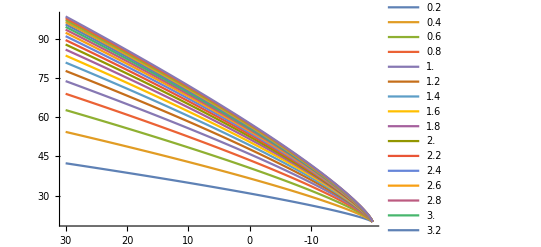

```mathematica
Plot[Evaluate[Table[TCalcPod[20,tOut,tOutDef[k],7.5,65],{k,0.2,4,0.2}]], {tOut, -30,20},PlotLegends->Placed[Range[0.2,4,0.2],Left],Ticks->{Table[{i,-i},{i,-30,20}],Automatic}]
```